```mathematica
If[StringTake[$SystemID,3]=="Win",
SetDirectory["C:\\Users\\pwrzo\\Documents\\GitHub\\AvoidedQP\\implementation\\"],
SetDirectory["~/Documents/GitHub/AvoidedQP/reimplementation/"]
]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/reimplementation

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
```

```mathematica
SetOptions[LinTicks,TickLengthScale->1.5];
```

```mathematica
t=1.0;
J=0.4t;
```

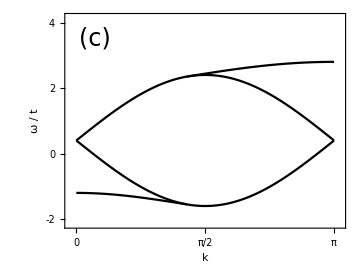

```mathematica
eye=Plot[{J+2t Sin[k],J-2t Sin[k]},{k,0,Pi},PlotStyle->Black,
PlotRange->{{0-1/42,1+1/42}*Pi,{-2.15,4.15}},
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,20],
PlotLegends->Placed[Automatic,Right],
AspectRatio->0.75,
FrameLabel->{"k",Style["ω / t"]},
Epilog->{
Text[
Style["(c)",Black,24,FontFamily->"Bookman Old Style"],
{Pi/14,3.5}]
},
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];
hump=Plot[{J+Sqrt[J^2+4t^2-4t J Cos[k]]},{k,3Pi/7,Pi},PlotStyle->Black,
PlotRange->{{0,Pi},{-2,6}},
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,20],
PlotLegends->Placed[Automatic,Right],
AspectRatio->0.75,
FrameLabel->{"k","ω"},
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];
pit=Plot[{J-Sqrt[J^2+4t^2-4t J Cos[k]]},{k,0,3Pi/7},PlotStyle->Black,
PlotRange->{{0-1/28,1+1/28}*Pi,{-2,6}},
Frame->True,Axes->False,
FrameStyle->Directive[Black,28,FontFamily->"Bookman Old Style"],
LabelStyle->Directive[Black,20],
PlotLegends->Placed[Automatic,Right],
AspectRatio->0.75,
FrameTicks->{{LinTicks,StripTickLabels[LinTicks]},{LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)],StripTickLabels[LinTicks[0,Pi,Pi/2,7,TickLabelFunction->(Rationalize[#/Pi]*Pi&)]]}}
];
Fig1c=Show[{eye,hump,pit},ImageSize->Medium]
Clear[t,J]
```

```mathematica
fileName=StringJoin["plots/",head,"/Fig_1-c.jpg"];
Export[fileName,Fig1c,ImageResolution->300]
```

plots/spc/Fig_1-c.jpg